### General definitions

```mathematica
<<(NotebookDirectory[]<>"ConstructKWalls_large_v3.m")
```

```mathematica
(* old parametrization from SW1 *)
```

```mathematica
f=(x-1)(x+1)(x-u)//Expand
```

u-x-u x^2+x^3

```mathematica
f=Collect[(f/.{x->(x+u/3)})//Expand,x]
```

(2 u)/3-(2 u^3)/27+(-1-u^2/3) x+x^3

```mathematica
(* new parametrization from SW2 *)
```

```mathematica
f=(4 x^3-4u x^2-x)/.{x->x+u/3}
```

-u/3-x-4 u (u/3+x)^2+4 (u/3+x)^3

```mathematica
f/.{x->-ⅈ}//Expand
```

5 ⅈ-u/3+(4 ⅈ u^2)/3-(8 u^3)/27

```mathematica
Collect[%//Expand,x]
```

5 ⅈ-u/3+(4 ⅈ u^2)/3-(8 u^3)/27

```mathematica
gg2=u↦-(-1-(4 u^2)/3);(*4+(4 u^2)/3;*)
gg3=u↦-(-u/3-(8 u^3)/27);(*(8 u)/3-(8 u^3)/27;*)

verb=False;
showlabels=True;
pltrng=2.5{{-1,1},{-1,1}};

θ=0(0.65-π/8);
step=0.01;
Λ0=0.05;
Λ=6;
MaxRank=10;  (* Level of the filtration *)
```

### Single θ

```mathematica
?BuildKWalls
```

BuildKWalls[n_] where n is the number of iterations 
for generating children walls. 
To plot use the command PlotKWalls. 
See also the commands trajs, paths, ints, genealogy, 
singpts, PlotMSWalls, MakeVideo, ScanTheta,
AllParticles, BPSspectrum, MSpts

```mathematica
generations=1;
```

```mathematica
BuildKWalls[generations]
```

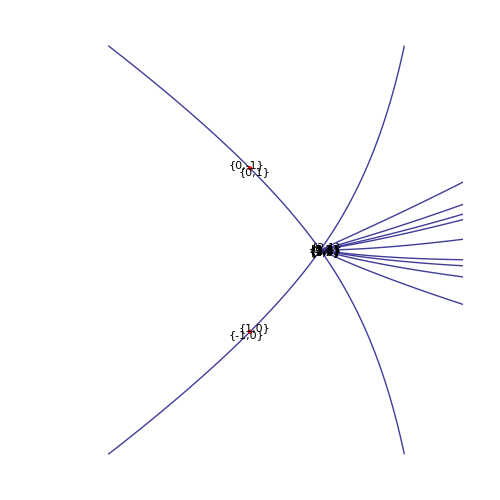

```mathematica
PlotKWalls
```

```mathematica
trajs⟦1,1,100⟧
```

1.74428+1.91268 ⅈ

```mathematica
singpts
```

{0.-1. ⅈ,0.+1. ⅈ}

```mathematica
trajs//Length
```

13

```mathematica
AllParticles//Column
```

{{1,0},1}
{{-1,0},1}
{{0,1},1}
{{0,-1},1}
{{1,2},1}
{{2,3},1}
{{3,4},1}
{{4,5},1}
{{1,1},-2}
{{5,4},1}
{{4,3},1}
{{3,2},1}
{{2,1},1}

```mathematica
?ints
ints//Column
```

Organized as follows {{tr1,poin1},{tr2,pt2},u},...} 
For example {{{1,1161},{2,1139},5.742-6.706 ⅈ},...}

{{1,64},{3,64},0.860368-1.49507×10^-9 ⅈ,2}

```mathematica
?genealogy
genealogy
```

Keeps info on who are the parents of a K-wall, 
the primary walls have no parents.
For example {{},{},{},{1,2},{1,3}}

{{},{},{},{},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3},{1,3}}

### Scanning θ

```mathematica
?ScanTheta
```

Use as ScanTheta[steps, filename, generations] 
by giving the positive integer steps, the string containing the filename, 
the number of generations.

```mathematica
directorypath=NotebookDirectory[]<>"media/";
CreateDirectory[directorypath];
```

```mathematica
folder=directorypath;
name="frame-SU2"
```

frame-SU2

```mathematica
steps=100;
generations=3; (* generation of K-walls genealogy *)
ScanTheta[steps,folder<>name,generations]
```

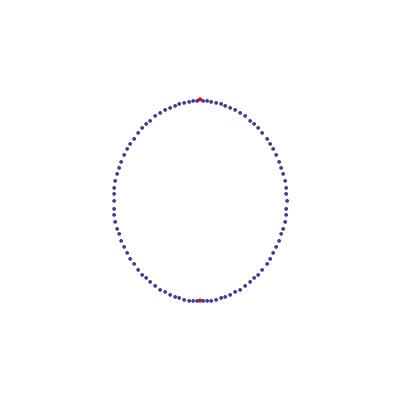

```mathematica
PlotMSWalls[folder]
```

```mathematica
MakeVideo[folder<>name]
```

```mathematica
?PlotCentralCharge
```

Use as PlotCentralCharge[n] where n=1,...,NPrimKWalls/2. 
This plots the real and imaginary parts of Z_n.

```mathematica
PlotCentralCharge[1]
```

#### strong coupling spectrum

```mathematica
u=0;
range=0.1;
```

```mathematica
BPSspectrum[u,folder,range]
```

total counts 14

{{{1,0},1},{{0,-1},1}}

#### weak coupling spectrum

```mathematica
u=2;
range=0.1;
```

```mathematica
BPSspectrum[u,folder,range]
```

total counts 20

{{{1,1},-2},{{3,4},1},{{4,5},1},{{2,3},1},{{1,2},1},{{0,1},1},{{-1,0},1},{{-2,-1},1},{{-3,-2},1},{{-5,-4},1},{{-4,-3},1},{{-1,-1},-2}}

```mathematica
%//Length
```

12